```mathematica
SetDirectory[ToFileName[("FileName"/.NotebookInformation[EvaluationNotebook[]])[[1]]]];
Clear[Header,FileData12,len,f];f=Import["tests1+3.csv"];
FileData12=Take[f,{2,55001}];Header=Take[f,1];Clear[f]; f=Import["test_stat1+2-2.csv"];FileData13=Take[f,{2,55001}];Clear[f];Header
```

{{N,H1,H0,T1,T2,T3,T4 (max run),T5,T6(0),T8,K[+],K[-],Kdiff,PValue,Evalue,Keys,Error}}

```mathematica
len12 = Length[FileData12];len13 = Length[FileData13];{len12,len13}
```

{55000,55000}

```mathematica
Err1=Select[FileData12,#[[17]]≠0 &]; Pe12=N[Length[Err1]/(len12*20000)];Join[Header, Err1] // MatrixForm
```

(N | H1 | H0 | T1 | T2 | T3 | T4 (max run) | T5 | T6(0) | T8 | K[+] | K[-] | Kdiff | PValue | Evalue | Keys | Error)

```mathematica
Err2=Select[FileData13,#[[17]]≠0 &]; Pe13=N[Length[Err2]/(len13*20000)];Join[Header, Err2] // MatrixForm
```

(N | H1 | H0 | T1 | T2 | T3 | T4 (max run) | T5 | T6(0) | T8 | K[+] | K[-] | Kdiff | PValue | Evalue | Keys | Error
1196 | 0.999002 | 1.05469 | 10372 | 39.5072 | 173 | 15 | 2495 | 0.0186 | 2.74448 | 4.5853 | 3.00416 | 1.58114 | 0.73273 | 34.088 | 12 | 21
40877 | 0.999086 | 1.0523 | 10356 | 49.3056 | 177 | 12 | 2494 | 0.0178 | 2.82296 | 4.26907 | 3.16228 | 1.1068 | 0.86377 | 30.4 | 12 | 21
49054 | 0.999106 | 1.0517 | 10352 | 39.392 | 146 | 14 | 2495 | 0.0176 | 2.82465 | 6.7989 | 1.89737 | 4.90153 | 0.62663 | 36.544 | 12 | 21)

```mathematica
{Pe12,Pe13}
```

{0.,2.72727×10^-9}

```mathematica
{{Min[FileData12[[All,10]]],Max[FileData12[[All,10]]]},{Min[FileData13[[All,10]]],Max[FileData13[[All,10]]]}}//MatrixForm
```

(4.10711 | 4.33029
2.63659 | 2.83941)

```mathematica
{{Min[FileData12[[All,5]]],Max[FileData12[[All,5]]]},{Min[FileData13[[All,5]]],Max[FileData13[[All,5]]]}}//MatrixForm
```

(4.7488 | 34.56
2.0608 | 55.6288)

```mathematica
{{Min[FileData12[[All,2]]],Min[FileData12[[All,3]]]},{Min[FileData13[[All,2]]],Min[FileData13[[All,3]]]}} // MatrixForm
```

(0.999801 | 0.976248
0.999002 | 0.969593)

```mathematica
{{Min[FileData12[[All,14]]],Max[FileData12[[All,14]]]},{Min[FileData13[[All,14]]],Max[FileData13[[All,14]]]}} // MatrixForm
```

(0.75049 | 1.
0.28036 | 1.)

```mathematica
Ent12=Select[FileData12,#[[2]]<0.99913 &];Ent13=Select[FileData13,#[[2]]<0.99913 &];{Length[Ent12],Length[Ent13]}
```

{0,3}

```mathematica
PVal12=Select[FileData12,#[[14]]<0.8&];PVal13=Select[FileData13,#[[14]]<0.8&];{Length[PVal12],Length[PVal13]}
```

{67,537}

```mathematica
K012=Select[FileData12,#[[13]]==0 &];K013=Select[FileData13,#[[13]]==0 &];{Length[K012],Length[K013]}
```

{1954,2624}

```mathematica
{Min[FileData12[[All,14]]],Max[FileData13[[All,14]]]}
```

{0.75049,1.}

```mathematica
P1=Select[FileData12,#[[14]]==1&];Length[P1]
```

1147

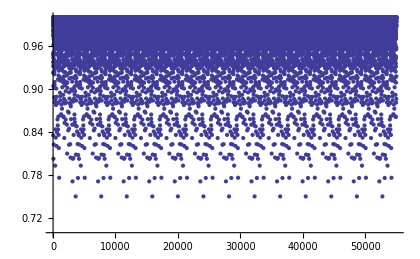
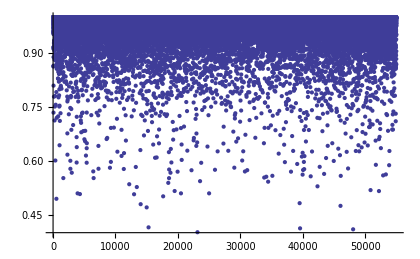
Chi Square Test (P-Value) generic PRNG | Chi Square Test (P-Value) QEKG
-Graphics- | -Graphics-

```mathematica
Grid[{{"Chi Square Test (P-Value) generic PRNG","Chi Square Test (P-Value) QEKG"},{ListPlot[FileData12[[All,14]],PlotRange->{0.7,1}, ImageSize->{420,300}],ListPlot[FileData13[[All,14]],PlotRange->{0.4,1},ImageSize->{420,300}]}} ,Frame->All]
```

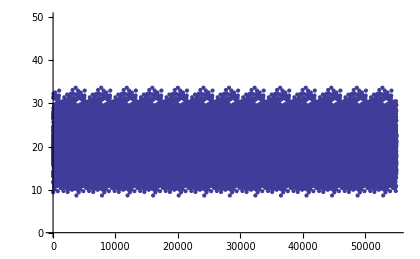
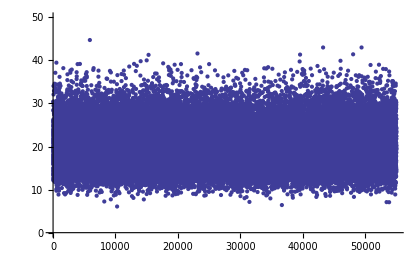
Chi Square Test (EValue) ENT | Chi Square Test (EValue) AMP
-Graphics- | -Graphics-

```mathematica
Grid[{{"Chi Square Test (EValue) ENT","Chi Square Test (EValue) AMP"},{ListPlot[FileData12[[All,15]],PlotRange->{0,50}, ImageSize->{420,300}],ListPlot[FileData13[[All,15]],PlotRange->{0,50},ImageSize->{420,300}]}} ,Frame->All]
```

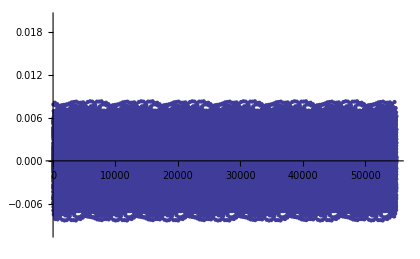
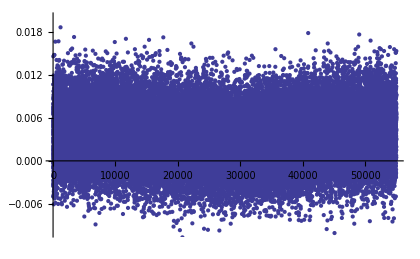
Test 6(0) ENT | Test 6(0) AMP
-Graphics- | -Graphics-

```mathematica
Grid[{{"Test 6(0) ENT","Test 6(0) AMP"},{ListPlot[FileData12[[All,9]],PlotRange->{-0.01,0.02}, ImageSize->{420,300}],ListPlot[FileData13[[All,9]],PlotRange->{-0.01,0.02},ImageSize->{420,300}]}} ,Frame->All]
```

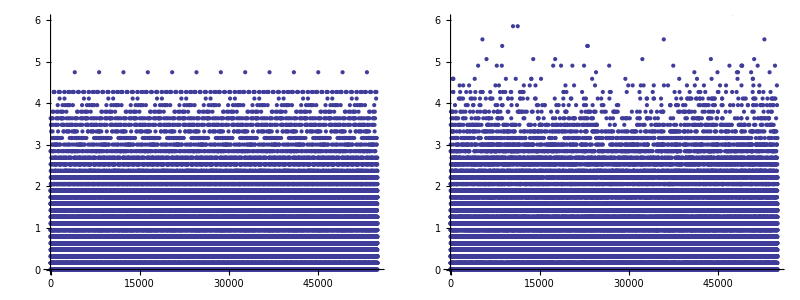

```mathematica
Grid[{{ListPlot[FileData12[[All,13]],PlotRange->{0,6}, ImageSize->{420,300}],ListPlot[FileData13[[All,13]],PlotRange->{0,6},ImageSize->{420,300}]}} ,Frame->All]
```

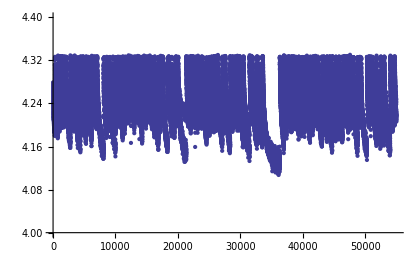
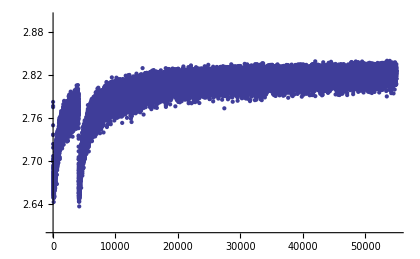
Test 8 ENT | Test 8 AMP
-Graphics- | -Graphics-

```mathematica
Grid[{{"Test 8 ENT","Test 8 AMP"},{ListPlot[FileData12[[All,10]],PlotRange->{4.0,4.4}, ImageSize->{420,300}],ListPlot[FileData13[[All,10]],PlotRange->{2.6,2.9},ImageSize->{420,300}]}} ,Frame->All]
```

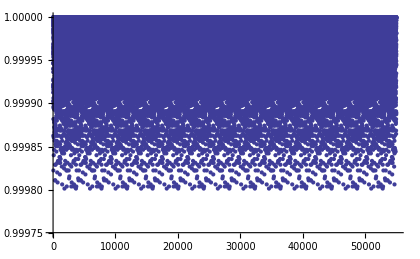
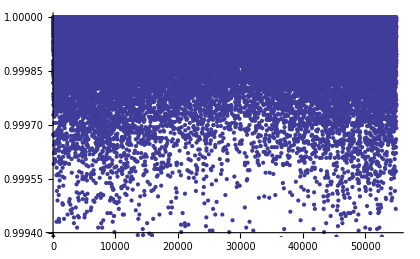
Entropy Cellular generic PRNG | Entropy QEKG
-Graphics- | -Graphics-

```mathematica
Grid[{{"Entropy Cellular generic PRNG","Entropy QEKG"},{ListPlot[FileData12[[All,2]],PlotRange->{0.99975,1}, ImageSize->{420,300}],ListPlot[FileData13[[All,2]],PlotRange->{0.9994,1},ImageSize->{420,300}]}} ,Frame->All]
```

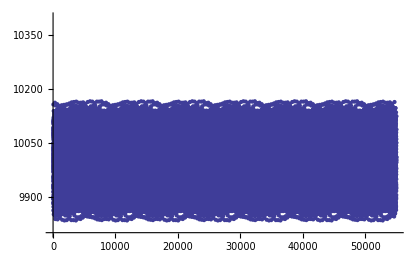
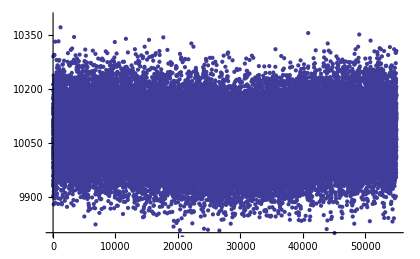
Monobit Test [FI140-1] (T1) generic PRNG | Monobit Test [FI140-1] (T1) QEKG
-Graphics- | -Graphics-

```mathematica
Grid[{{"Monobit Test [FI140-1] (T1) generic PRNG", "Monobit Test [FI140-1] (T1) QEKG"},{ListPlot[FileData12[[All,4]],PlotRange->{9800,10400}, ImageSize->{420,300}],ListPlot[FileData13[[All,4]],PlotRange->{9800,10400},ImageSize->{420,300}]}} ,Frame->All]
```

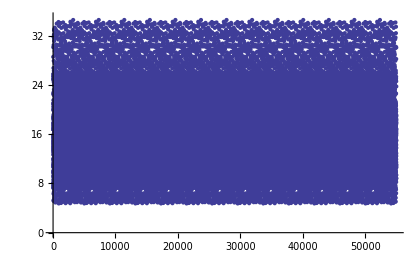
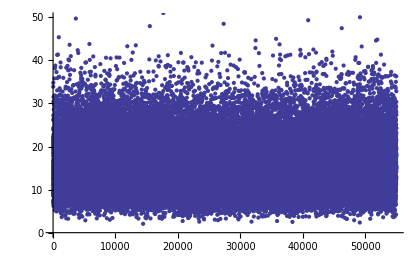
Block Test (T2) generic PRNG | Block Test (T2) QEKG
-Graphics- | -Graphics-

```mathematica
Grid[{{"Block Test (T2) generic PRNG", "Block Test (T2) QEKG"},{ListPlot[FileData12[[All,5]],PlotRange->{0,35}, ImageSize->{420,300}],ListPlot[FileData13[[All,5]],PlotRange->{0,50},ImageSize->{420,300}]}} ,Frame->All]
```